```mathematica
Clear["Global`*"];
ubulk=1;umem =1;EDiffMax = 0.1;
```

## Energy functions

```mathematica
Lbulk[ϕ_,tbulk_,μb_]:=(tbulk/2)ϕ^2+(ubulk/4!)ϕ^4 - μb(ϕ);
ϕb[tbulk_,μb_]:=ϕ/.FindMinimum[Lbulk[ϕ,tbulk,μb],{ϕ,0}][[2]];
μbulk[tbulk_,ϕb_] := (1/6) (6 tbulk ϕb+ϕb^3)
gradbulk[ϕ_,ϕbulk_,μb_]:= -(ϕ-ϕbulk)Surd[(ubulk/12)(ϕ + ϕbulk)^2 + (μb/ϕbulk),2];
Hb[ϕ1_,ϕbulk_,μb_]:=NIntegrate[gradbulk[ϕ,ϕbulk,μb],{ϕ,ϕ1,ϕbulk}];
Hψ[ψ_,tmem_]:=(tmem/2)ψ^2+(umem/4!)ψ^4;
fρ[ρ_] := -1/4-(5 ρ)/6+(3 ρ^2)/2-ρ^3/2+ρ^4/12;
Hint[ψ_,ρ_,ϕ1_,hψ_,hϕ_]:=-(hψ)(ψ)(ρ)- (hϕ)(ϕ1)(ρ);
Hsurface[ϕ1_,ψ_,ρ_,tmem_,ϕbulk_,μb_,λρ_,λψ_,hψ_,hϕ_]:=
Hψ[ψ,tmem]+Hint[ψ,ρ,ϕ1,hψ,hϕ]- (λρ(ρ))- (λψ(ψ)) + Hb[ϕ1,ϕbulk,μb] + fρ[ρ];

Hmembrane[ϕ1_,ψ_,ρ_,tmem_,λρ_,λψ_,hψ_,hϕ_]:=
Hψ[ψ,tmem]+Hint[ψ,ρ,ϕ1,hψ,hϕ]- λρ(ρ)- λψ(ψ)  + fρ[ρ];
ϕDeriv[ϕ1_ ,ρ_,ϕbulk_,hϕ_,μb_]:= -hϕ ρ-(-ϕ1+ϕbulk) (μb/ϕbulk+1/12 (ϕ1+ϕbulk)^2)^(1/2);
ψDeriv[ψ_,ρ_,hψ_,λψ_,tmem_] := -λψ-hψ ρ+tmem ψ+ψ^3/6;
ρDeriv[ρ_ ,ϕ1_,ψ_,λρ_,hϕ_,hψ_]:= -5/6-λρ+3 ρ-(3 ρ^2)/2+ρ^3/3-hϕ ϕ1-hψ ψ;
```

Surface variable: tmem - membrane temp, λψ - membrane chem potent, hψ - tether-membrane coupling

Bulk Variable: tbulk - bulk temp, μb - bulk chemical potential,ϕbulk = bulk equilibrium density, hϕ = tether-bulk coupling

Tether variables:; λρ - tether chemical potential

## Functions for calculations

#### If 3 minima exist, computes the energy difference between all 3 solutions - used for finding the 3 Phase region Assigns number of solutions based on where they are in relation to 3 Phase

```mathematica
FindAllPhase[λρ_,λψ_] :=
Module[{sol1,sol2,sol3,E2,E3},
sol1 = {};sol2={};sol3={};
E2 = ∞;E3 = ∞;
MinSols = NSolve[{ϕDeriv[ϕ1 ,ρ,ϕbulk,hϕ,μb]== ψDeriv[ψ,ρ,hψ,λψ,tmem]== ρDeriv[ρ,ϕ1,ψ,λρ,hϕ,hψ]== 0},
{ρ,ψ,ϕ1},Reals];
Ediff = ∞;E13 = ∞;E15 =∞;E35 = ∞;
ϕ1Tab  = ϕ1/. MinSols;ρTab  = ρ/. MinSols;ψTab  = ψ/. MinSols;
NSols =Length[MinSols];
Energies = Table[Hsurface[ϕ1Tab[[k]], ψTab[[k]],  ρTab[[k]], tmem,ϕbulk ,μb,λρ,λψ,hψ,hϕ],{k,1,NSols}];

If[NSols== 5,
Earr = {Energies[[1]],Energies[[3]],Energies[[5]]};
minE = Min[Earr];pos  = Position[Earr,minE][[1,1]];
If[pos ==1,
EdiffArr = {Abs[Energies[[1]] - Energies[[3]]],Abs[Energies[[1]]  - Energies[[5]]]};
minEdiff = Min[EdiffArr];posEdiff = Position[EdiffArr,minEdiff][[1,1]];
If[minEdiff < EDiffMax && posEdiff == 1,
sol2 ={λρ,λψ,ϕ1Tab[[1]],ψTab[[1]],ρTab[[1]],ϕ1Tab[[3]],ψTab[[3]],ρTab[[3]],minEdiff,13};
E2 = minEdiff;
];
If[minEdiff < EDiffMax && posEdiff == 2,
sol2 ={λρ,λψ,ϕ1Tab[[1]],ψTab[[1]],ρTab[[1]],ϕ1Tab[[5]],ψTab[[5]],ρTab[[5]],minEdiff,15};
E2 = minEdiff;
];
If[minEdiff > EDiffMax,
sol1 = {λρ,λψ,ϕ1Tab[[1]],ψTab[[1]],ρTab[[1]],1};
];

];
If[pos ==3,
EdiffArr = {Abs[Energies[[3]] - Energies[[1]]],Abs[Energies[[3]]  - Energies[[5]]]};
minEdiff = Min[EdiffArr];posEdiff = Position[EdiffArr,minEdiff][[1,1]];
If[minEdiff < EDiffMax && posEdiff == 1,
sol2 ={λρ,λψ,ϕ1Tab[[1]],ψTab[[1]],ρTab[[1]],ϕ1Tab[[3]],ψTab[[3]],ρTab[[3]],minEdiff,13};
E2 = minEdiff;
];
If[minEdiff < EDiffMax && posEdiff == 2,
sol2 ={λρ,λψ,ϕ1Tab[[3]],ψTab[[3]],ρTab[[3]],ϕ1Tab[[5]],ψTab[[5]],ρTab[[5]],minEdiff,35};
E2 = minEdiff;
];
If[minEdiff > EDiffMax,
sol1 = {λρ,λψ,ϕ1Tab[[3]],ψTab[[3]],ρTab[[3]],3};];
];
If[pos ==5,
EdiffArr = {Abs[Energies[[5]] - Energies[[1]]],Abs[Energies[[5]]  - Energies[[3]]]};
minEdiff = Min[EdiffArr];posEdiff = Position[EdiffArr,minEdiff][[1,1]];
If[minEdiff < EDiffMax && posEdiff == 1,
sol2 ={λρ,λψ,ϕ1Tab[[1]],ψTab[[1]],ρTab[[1]],ϕ1Tab[[5]],ψTab[[5]],ρTab[[5]],minEdiff,15};
E2 = minEdiff;
];
If[minEdiff <EDiffMax && posEdiff == 2,
sol2 ={λρ,λψ,ϕ1Tab[[3]],ψTab[[3]],ρTab[[3]],ϕ1Tab[[5]],ψTab[[5]],ρTab[[5]],minEdiff,35};
E2 = minEdiff;
];
If[minEdiff > EDiffMax,
sol1 = {λρ,λψ,ϕ1Tab[[5]],ψTab[[5]],ρTab[[5]],5};];
];
Ediff3Phase = Abs[Energies[[1]] - Energies[[3]]] + Abs[Energies[[1]] - Energies[[5]]] + Abs[Energies[[3]] - Energies[[5]]];
E3 = Ediff3Phase;
sol3={λρ,λψ,ϕ1Tab[[1]],ψTab[[1]],ρTab[[1]],ϕ1Tab[[3]],ψTab[[3]],ρTab[[3]],ϕ1Tab[[5]],ψTab[[5]],ρTab[[5]],Ediff3Phase};
];

If[NSols == 3,
Ediff = Abs[Energies[[1]] - Energies[[3]]];
If[Ediff < EDiffMax,
sol2 ={λρ,λψ,ϕ1Tab[[1]],ψTab[[1]],ρTab[[1]],ϕ1Tab[[3]],ψTab[[3]],ρTab[[3]],Ediff,0};
E2 = Ediff;,
MinE = Min[Energies];
pos = Position[Energies,MinE][[1,1]];
sol1 = {λρ,λψ,ϕ1Tab[[pos]],ψTab[[pos]],ρTab[[pos]],1};];
];
If[NSols== 1,
sol1 = {λρ,λψ,ϕ1Tab[[1]],ψTab[[1]],ρTab[[1]],1};
];
{sol1,sol2,sol3,E2,E3}
];

MakeTables[solsTable_] := 
Module[{ψρTable1Phase,ψρTables2Phase,ψρTable3Phase,ϕ1sTable1Phase,ϕ1sTable2Phase,ϕ1sTable3Phase,λsTable2Phase,λ3Phase,λs1Phase},
ϕ1sTable1Phase ={};ϕ1sTable2Phase ={{},{},{}};
λsTable2Phase ={{},{},{}};
ψρTable1Phase={};ψρTables2Phase= {{},{},{}};λs1Phase = {};
(*Find three phase point*)
sol3PhaseEnergies = solsTable[[;;,;;,5]];
minE = Min[sol3PhaseEnergies];
If[minE < 1,
minPos = Position[sol3PhaseEnergies,minE][[1]];
ϕ1sTable3Phase = {solsTable[[minPos[[1]],minPos[[2]],3,3]],
solsTable[[minPos[[1]],minPos[[2]],3,6]],
solsTable[[minPos[[1]],minPos[[2]],3,9]]};
ψρTable3Phase = {{solsTable[[minPos[[1]],minPos[[2]],3,4]],solsTable[[minPos[[1]],minPos[[2]],3,5]]},{solsTable[[minPos[[1]],minPos[[2]],3,7]],solsTable[[minPos[[1]],minPos[[2]],3,8]]},{solsTable[[minPos[[1]],minPos[[2]],3,10]],solsTable[[minPos[[1]],minPos[[2]],3,11]]}};
λ3Phase ={solsTable[[minPos[[1]],minPos[[2]],3,2]],solsTable[[minPos[[1]],minPos[[2]],3,1]]};
,
ψρTable3Phase = {{∞,∞},{∞,∞},{∞,∞}};
];

For [i =1,i ≤ Length [solsTable], i++,
For[j=1,j ≤ Length[solsTable[[i]]], j++,
sol1 =solsTable[[i,j,1]];
sol2 =solsTable[[i,j,2]];

If[Length[sol2] == 0 && Length[sol1] > 4,
AppendTo[ϕ1sTable1Phase,sol1[[3]]];
AppendTo[ψρTable1Phase,{sol1[[4]],sol1[[5]]}];
AppendTo[λs1Phase,{sol1[[2]],sol1[[1]]}];
];

If[Length[sol2] == 10,
If[sol2[[10]] == 13 && sol2[[1]] < λ3Phase[[2]],
AppendTo[ψρTables2Phase[[1]],{{sol2[[4]],sol2[[5]]},{sol2[[7]],sol2[[8]]}}]; 
AppendTo[λsTable2Phase[[1]],{sol2[[2]],sol2[[1]]}];
AppendTo[ϕ1sTable2Phase[[1]],{sol2[[3]],sol2[[6]]}];
];
If[sol2[[10]] == 15,
AppendTo[ψρTables2Phase[[2]],{{sol2[[4]],sol2[[5]]},{sol2[[7]],sol2[[8]]}}];
AppendTo[λsTable2Phase[[2]],{sol2[[2]],sol2[[1]]}]; 
AppendTo[ϕ1sTable2Phase[[2]],{sol2[[3]],sol2[[6]]}];
];
If[sol2[[10]] == 35,
AppendTo[ψρTables2Phase[[3]],{{sol2[[4]],sol2[[5]]},{sol2[[7]],sol2[[8]]}}];
AppendTo[λsTable2Phase[[3]],{sol2[[2]],sol2[[1]]}]; 
AppendTo[ϕ1sTable2Phase[[3]],{sol2[[3]],sol2[[6]]}];
];
If[sol2[[10]] == 0,
(*In 2 Phase TD-TL All ρs > and ψs in between 1 and 3*)
If[ψρTable3Phase[[1,2]] > sol2[[5]] && ψρTable3Phase[[2,2]] > sol2[[8]] && ψρTable3Phase[[3,2]] > sol2[[5]] ,
AppendTo[ψρTables2Phase[[1]],{{sol2[[4]],sol2[[5]]},{sol2[[7]],sol2[[8]]}}];
AppendTo[λsTable2Phase[[1]],{sol2[[2]],sol2[[1]]}];
AppendTo[ϕ1sTable2Phase[[1]],{sol2[[3]],sol2[[6]]}];
];
(*in TD-TE all ψs gt and ρ gets larger than TD*)
If[ψρTable3Phase[[1,1]]> sol2[[4]] && ψρTable3Phase[[1,2]] < sol2[[8]],
AppendTo[ψρTables2Phase[[2]],{{sol2[[4]],sol2[[5]]},{sol2[[7]],sol2[[8]]}}];
AppendTo[λsTable2Phase[[2]],{sol2[[2]],sol2[[1]]}];
AppendTo[ϕ1sTable2Phase[[2]],{sol2[[3]],sol2[[6]]}];
];
(*In TE-TL all ψs < and *)
If[ψρTable3Phase[[2,1]] < sol2[[4]] && ψρTable3Phase[[3,1]] < sol2[[7]],
AppendTo[ψρTables2Phase[[3]],{{sol2[[4]],sol2[[5]]},{sol2[[7]],sol2[[8]]}}];
AppendTo[λsTable2Phase[[3]],{sol2[[2]],sol2[[1]]}];
AppendTo[ϕ1sTable2Phase[[3]],{sol2[[3]],sol2[[6]]}];
]; 
];
];
];
];
{ϕ1sTable1Phase,ϕ1sTable2Phase ,ϕ1sTable3Phase,ψρTable1Phase,ψρTables2Phase,ψρTable3Phase,λsTable2Phase,λ3Phase,λs1Phase}
];
```

#### Density profile function for plotting

```mathematica
DensityProfile[ϕ1_,ϕbulk_,μb_] :=
Module[{densityProf},
densityProf = ConstantArray[0,100];
densityProf[[1]] = ϕ1;dz = 0.1;
For[i =2,i ≤ 100, i++,
dϕ = gradbulk[densityProf[[i-1]],ϕbulk,μb]*dz;
densityProf[[i]] = densityProf[[i-1]]+dϕ;
];
densityProf
];
```

## Calculate phase diagram over λ_ρ,λ_ψ Values Fixing other parameters

```mathematica
(*Parameters for Figure 6, three phase coexistence region*)
 hϕ=1;hψ =1;tmem = -0.2;tbulk=-0.4; ubulk=1;umem=1; 
ϕbulk = -2;μb = μbulk[tbulk,ϕbulk];
λρ3Phase = None;λψ3Phase = None;
If[λρ3Phase== None,λρ3Phase = -2;];If[λψ3Phase == None,λψ3Phase=2;];
E5 = ∞;dρ = 0.1;dψ = 0.1;δψ =2;δρ = 2;
λρs =Table[i,{i,λρ3Phase-δρ,λρ3Phase + δρ,dρ}];
λψs = Table[i,{i,λψ3Phase - δψ,λψ3Phase+ δψ,dψ}];

(*Parameters near Prewetting Critical point *)
(*tmem= 1.2;tbulk=2;ϕbulk=-2;μb = μbulk[tbulk,ϕbulk]
λρ =0.3; λψ =0.7;*)
Off[NSolve::ratnz];Off[NIntegrate::nlim]
phasesAll=ParallelTable[FindAllPhase[λρ,λψ],{λρ,λρs},{λψ,λψs}];
{ϕ1sTable1Phase,ϕ1sTable2Phase ,ϕ1sTable3Phase,ψρTable1Phase,ψρTables2Phase,ψρTable3Phase,λsTable2,λ3Phase,λs1Phase}=  MakeTables[phasesAll];
λρ3Phase= λ3Phase[[2]] ;λψ3Phase = λ3Phase[[1]];
```

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

## Demonstrates Gradient Construction at each Coexistence region

```mathematica
solTab =NSolve[{ϕDeriv[ϕ1 ,ρ,ϕbulk,hϕ,μb]== ψDeriv[ψ,ρ,hψ,λψ3Phase,tmem]== ρDeriv[ρ,ϕ1,ψ,λρ3Phase,hϕ,hψ]== 0},
{ρ,ψ,ϕ1},Reals];
ϕ13Phase = ϕ1 /. solTab ; ψ3Phase= ψ /. solTab;  ρ3Phase= ρ /. solTab;
λρPlot1 = -3.96;λψPlot1 = 1.37;
λρPlot3  = -1.44; λψPlot3 = 0.48
λρPlot2  = -2.65; λψPlot2 = 3.0;

solPlot1 = NSolve[{ϕDeriv[ϕ1 ,ρ,ϕbulk,hϕ,μb]== ψDeriv[ψ,ρ,hψ,λψPlot1,tmem]== ρDeriv[ρ,ϕ1,ψ,λρPlot1,hϕ,hψ]== 0},
{ρ,ψ,ϕ1},Reals];
ψSol1 = ψ /. solPlot1;
ρSol1 = ρ /. solPlot1;
ϕ1Plot1 = ϕ1 /. solPlot1;
solPlot2 = NSolve[{ϕDeriv[ϕ1 ,ρ,ϕbulk,hϕ,μb]== ψDeriv[ψ,ρ,hψ,λψPlot2,tmem]== ρDeriv[ρ,ϕ1,ψ,λρPlot2,hϕ,hψ]== 0},
{ρ,ψ,ϕ1},Reals];
ψSol2 = ψ /. solPlot2;
ρSol2 = ρ /. solPlot2;
ϕ1Plot2 = ϕ1 /. solPlot2;
solPlot3 = NSolve[{ϕDeriv[ϕ1 ,ρ,ϕbulk,hϕ,μb]== ψDeriv[ψ,ρ,hψ,λψPlot3,tmem]== ρDeriv[ρ,ϕ1,ψ,λρPlot3,hϕ,hψ]== 0},
{ρ,ψ,ϕ1},Reals];
ψSol3 = ψ /. solPlot3;
ρSol3 = ρ /. solPlot3;
ϕ1Plot3 = ϕ1 /. solPlot3;

ψSols1[ϕ1_] :=ψ /.NSolve[{D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot1,λψPlot1,hψ,hϕ],ρ] == 0,D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot1,λψPlot1,hψ,hϕ],ψ] == 0  },{ρ,ψ}];
ρSols1[ϕ1_]:= ρ/.NSolve[{D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot1,λψPlot1,hψ,hϕ],ρ] == 0,D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot1,λψPlot1,hψ,hϕ],ψ] == 0  },{ρ,ψ}];
ψSols2[ϕ1_] :=ψ /.NSolve[{D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot2,λψPlot2,hψ,hϕ],ρ] == 0,D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot2,λψPlot2,hψ,hϕ],ψ] == 0  },{ρ,ψ}];
ρSols2[ϕ1_]:= ρ/.NSolve[{D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot2,λψPlot2,hψ,hϕ],ρ] == 0,D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot2,λψPlot2,hψ,hϕ],ψ] == 0  },{ρ,ψ}];
ψSols3[ϕ1_] :=ψ /.NSolve[{D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot3,λψPlot3,hψ,hϕ],ρ] == 0,D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot3,λψPlot3,hψ,hϕ],ψ] == 0  },{ρ,ψ}];
ρSols3[ϕ1_]:= ρ/.NSolve[{D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot3,λψPlot3,hψ,hϕ],ρ] == 0,D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρPlot3,λψPlot3,hψ,hϕ],ψ] == 0  },{ρ,ψ}];
ψSols3Phase[ϕ1_] :=ψ /.NSolve[{D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρ3Phase,λψ3Phase,hψ,hϕ],ρ] == 0,D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρ3Phase,λψ3Phase,hψ,hϕ],ψ] == 0  },{ρ,ψ}];
ρSols3Phase[ϕ1_]:= ρ/.NSolve[{D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρ3Phase,λψ3Phase,hψ,hϕ],ρ] == 0,D[Hsurface[ϕ1,ψ,ρ,tmem,ϕbulk,μb,λρ3Phase,λψ3Phase,hψ,hϕ],ψ] == 0  },{ρ,ψ}];
HsurftoPlot1 = Table[N@D[Hmembrane[ϕ1,ψSols1[ϕ1][[i]],ρSols1[ϕ1][[i]], tmem,λρPlot1,λψPlot1,hψ,hϕ],ϕ1],{i,1,Length[ψSols1[ϕ1]]}];
HsurftoPlot2 = Table[N@D[Hmembrane[ϕ1,ψSols2[ϕ1][[i]],ρSols2[ϕ1][[i]], tmem,λρPlot2,λψPlot2,hψ,hϕ],ϕ1],{i,1,Length[ψSols2[ϕ1]]}];
HsurftoPlot3 = Table[N@D[Hmembrane[ϕ1,ψSols3[ϕ1][[i]],ρSols3[ϕ1][[i]], tmem,λρPlot3,λψPlot3,hψ,hϕ],ϕ1],{i,1,Length[ψSols3[ϕ1]]}];
Hsurf3Phase = Table[N@D[Hmembrane[ϕ1,ψSols3Phase[ϕ1][[i]],ρSols3Phase[ϕ1][[i]], tmem,λρ3Phase,λψ3Phase,hψ,hϕ],ϕ1],{i,1,Length[ψSols3Phase[ϕ1]]}];
```

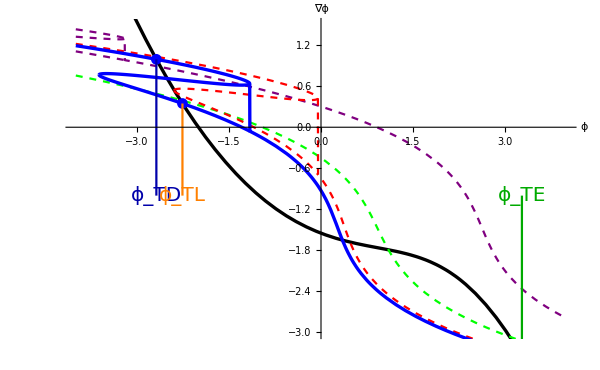

```mathematica
(*Full three phase graphical construtctions *)
p1 = Show[{Plot[gradbulk[ϕ1,ϕb[tbulk,μb],μb],{ϕ1,-4,4},PlotStyle->{Thickness[0.004],Black}],
Plot[HsurftoPlot1,{ϕ1,-4,4},PlotStyle->Table[{Dashed,Purple},{i,1,Length[HsurftoPlot1]}]],
Plot[HsurftoPlot2,{ϕ1,-4,4},PlotStyle->Table[{Dashed,Green},{i,1,Length[HsurftoPlot1]}]],
Plot[HsurftoPlot3,{ϕ1,-4,4},PlotStyle->Table[{Dashed,Red},{i,1,Length[HsurftoPlot1]}]],
Plot[Hsurf3Phase,{ϕ1,-4,4},PlotStyle->Table[{Thickness[0.004],Blue},{i,1,Length[HsurftoPlot1]}]],
ListPlot[{{ϕ13Phase[[1]],gradbulk[ϕ13Phase[[1]],ϕb[tbulk,μb],μb]},{ϕ13Phase[[3]],gradbulk[ϕ13Phase[[3]],ϕb[tbulk,μb],μb]},{ϕ13Phase[[5]],gradbulk[ϕ13Phase[[5]],ϕb[tbulk,μb],μb]}},PlotStyle->{{Blue},{Orange},{Darker[Green]}}],
ListLinePlot[{{ϕ13Phase[[1]],gradbulk[ϕ13Phase[[1]],ϕb[tbulk,μb],μb]},{ϕ13Phase[[1]],-1}},PlotStyle->{Darker[Blue]}],
ListLinePlot[{{ϕ13Phase[[3]],gradbulk[ϕ13Phase[[3]],ϕb[tbulk,μb],μb]},{ϕ13Phase[[3]],-1}},PlotStyle->{Orange}],
ListLinePlot[{{ϕ13Phase[[5]],gradbulk[ϕ13Phase[[5]],ϕb[tbulk,μb],μb]},{ϕ13Phase[[5]],-1}},PlotStyle->{Darker[Green]}]},
Epilog->{{Text[Style["ϕ_TD",20,Darker[Blue]],{ϕ13Phase[[1]],-1}]},{Text[Style["ϕ_TL",20,Orange],{ϕ13Phase[[3]],-1}]},{Text[Style["ϕ_TE",20,Darker[Green]],{ϕ13Phase[[5]],-1}]}},
PlotRange -> {All,{-3,1.5}},AxesLabel->{Style["ϕ",20,Bold,Black],Style["∇ϕ",20,Bold,Black]},AxesStyle-> Thickness[0.004],TicksStyle->Directive["Label", 14],ImageSize -> 600]
```

```mathematica
Export["./Surface_lines_three_phase.svg",p1/.Line[x_]:>Line@Split[x,Norm[#-#2]<0.5&]];
```

## Chemical Potential and ρ-ψ Plots

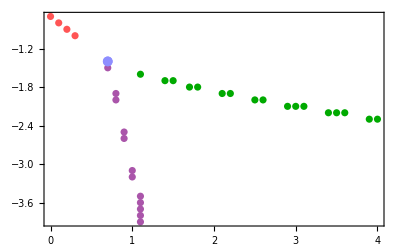
-Graphics-λ_ψλ_ρ

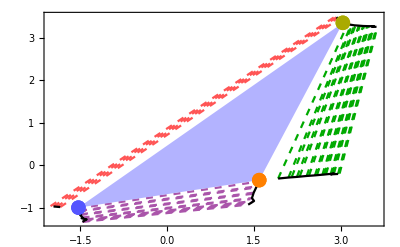
-Graphics-Membrane Composition, ψTether Composition, ρ

```mathematica
(*Chemical Potential Plot*)
Labeled[Show[ListPlot[λsTable2 /. {} -> {None,None},PlotStyle->{Lighter[Purple],Lighter[Red],Darker[Green]}],ListPlot[{{λψ3Phase,λρ3Phase}},PlotStyle->Lighter[Lighter[Blue]],PlotMarkers->{Graphics[Disk[{0,0},1]],10}],Frame-> True,PlotRange->{All,All}],{Subscript[λ,ψ],Subscript[λ,ρ]},{Bottom,Left},RotateLabel->True]

Labeled[Show[
ListLinePlot[ψρTables2Phase[[1]] /. {} -> {None,None},PlotStyle->Table[{Lighter[Purple],Dashed},{i,1,Length[ψρTables2Phase[[1]]]}]],
ListLinePlot[ψρTables2Phase[[2]] /. {} -> {None,None},PlotStyle->Table[{Lighter[Red],Dashed},{i,1,Length[ψρTables2Phase[[2]]]}]],
ListLinePlot[ψρTables2Phase[[3]] /. {} -> {None,None},PlotStyle->Table[{Darker[Green],Dashed},{i,1,Length[ψρTables2Phase[[3]]]}]],
ListLinePlot[{ψρTables2Phase[[1,;;,1]],ψρTables2Phase[[1,;;;; 2,2]],ψρTables2Phase[[2,;; ;; 2,1]],
ψρTables2Phase[[2,;; ;; 2,2]],ψρTables2Phase[[3,1;;;; 2,1]],ψρTables2Phase[[3,1;;;; 2,2]]},PlotStyle-> Black],
Graphics[{Lighter[Lighter[Lighter[Blue]]],Triangle[ψρTable3Phase]}],ListPlot[{ψρTable3Phase[[1]]},PlotStyle->{Lighter[Blue]},PlotMarkers->{Graphics[Disk[{0,0},1]],15}],
ListPlot[{ψρTable3Phase[[2]]},PlotStyle->{Orange},PlotMarkers->{Graphics[Disk[{0,0},1]],15}],
ListPlot[{ψρTable3Phase[[3]]},PlotStyle->{Darker[Yellow]},PlotMarkers->{Graphics[Disk[{0,0},1]],15}],
PlotRange-> All,AxesOrigin->{Min[ψρTables2Phase[[;;,;;,1]]],Min[ψρTables2Phase[[1,;;,1]]]},Frame -> True],{"Membrane Composition, ψ","Tether Composition, ρ"},{Bottom,Left},RotateLabel->True]
```

## ϕ(z) Density Profiles

```mathematica
solProfarr1 = DensityProfile[ϕ1sTable3Phase[[1]],ϕbulk,μb];
solProfarr2 = DensityProfile[ϕ1sTable3Phase[[2]],ϕbulk,μb];
solProfarr3 = DensityProfile[ϕ1sTable3Phase[[3]],ϕbulk,μb];
ListLinePlot[{solProfarr1 ,solProfarr2,solProfarr3},AxesLabel->{Style[z,20,FontFamily->"Courier"],Style[Subscript[ϕ,z],20,FontFamily->"Courier"]},AxesOrigin->{1,ϕbulk},PlotStyle-> {Lighter[Blue],Orange,Darker[Yellow]},PlotRange->{{1,100},All}]
```

## Plotting w/o 3 phase coexistence

```mathematica
Labeled[Show[ListPlot[λsTable2 /. {} -> {None,None},PlotStyle->{Lighter[Red]}],
Frame-> True,PlotRange->{All,All}],{Subscript[λ,ψ],Subscript[λ,ρ]},{Bottom,Left},RotateLabel->True]
Labeled[Show[
ListLinePlot[ψρTables2Phase[[2]] /. {} -> {None,None},PlotStyle->Table[{Lighter[Red],Dashed},{i,1,Length[ψρTables2Phase[[2]]]}]],
ListLinePlot[ψρTables2Phase[[1]] /. {} -> {None,None},PlotStyle->Table[{Lighter[Red],Dashed},{i,1,Length[ψρTables2Phase[[1]]]}]],
ListLinePlot[{ψρTables2Phase[[2,;;,1]] /. {}-> {None,None},ψρTables2Phase[[1,;;,2]] /. {}->  {None,None},ψρTables2Phase[[1,;;,1]]  /. {} -> {None,None},ψρTables2Phase[[2,;;,2]]} /. {} -> {None,None},PlotStyle-> Black],
PlotRange-> All,AxesOrigin->{Min[ψρTables2Phase[[;;,;;,1]]],Min[ψρTables2Phase[[;;,;;,1]]]},Frame -> True],{" ψ"," ρ"},{Bottom,Left},RotateLabel->True]
```

### Energy as a function of ϕ_0,ρ,ψ

```mathematica
ψSols1[ϕ1_] :=ψ /.NSolve[{D[Hsurface[ϕ1,ψ,ρ,a,ϕbulk,μb,λρ3Phase,λψ3Phase,hψ,hϕ,ρo],ρ] == 0,D[Hsurface[ϕ1,ψ,ρ,a,ϕbulk,μb,λρ3Phase,λψ3Phase,hψ,hϕ,ρo],ψ] == 0  },{ρ,ψ},Reals];
ρSols1[ϕ1_]:= ρ/.NSolve[{D[Hsurface[ϕ1,ψ,ρ,a,ϕbulk,μb,λρ3Phase,λψ3Phase,hψ,hϕ,ρo],ρ] == 0,D[Hsurface[ϕ1,ψ,ρ,a,ϕbulk,μb,λρ3Phase,λψ3Phase,hψ,hϕ,ρo],ψ] == 0  },{ρ,ψ},Reals];
(*Compute the energy of the membrane fixing ϕ1 to be its optimal value *)
ϕSols[ψ_,ρ_] := ϕ1 /. NSolve[D[Hsurface[ϕ1,ψ,ρ,a,ϕbulk,μb,λρ3Phase,λψ3Phase,hψ,hϕ,ρo],ϕ1] == 0 ,ϕ1,Reals][[1]];
HsurfMem[ψ_,ρ_] := Hsurface[ϕSols[ψ,ρ],ψ,ρ, a,ϕbulk,μb,λρ3Phase,λψ3Phase,hψ,hϕ,ρo];
```

```mathematica
Sols = NSolve[{ϕDeriv[ϕ1 ,ρ,ϕbulk,hϕ,μb]== ψDeriv[ψ,ρ,hψ,λψ3Phase,a]== ρDeriv[ρ,ϕ1,ψ,ρo,λρ3Phase,hϕ,hψ]== 0},
{ρ,ψ,ϕ1},Reals];
ϕ1s = ϕ1 /. Sols
ψs = ψ /. Sols
 ρs= ρ /. Sols
pts = {{ψs[[1]],ρs[[1]]},{ψs[[3]],ρs[[3]]},{ψs[[5]],ρs[[5]]}}
ψρPlot = Labeled[ContourPlot[HsurfMem[ψ,ρ],{ψ,-2,3.1},{ρ,-2,4},ColorFunction->"Pastel",Mesh->Full,BoundaryStyle->Directive[Gray,Thick],
Epilog->{{Line[{pts[[1]],pts[[2]]}],Dashed},{Line[{pts[[1]],pts[[3]]}],Dashed},{Line[{pts[[2]],pts[[3]]}],Dashed},{PointSize[0.03],Purple, Point[pts[[1]]],Orange,Point[pts[[2]]],Darker[Green], Point[pts[[3]]]}}],
{Style["ψ",Bold,Black,20],Style["ρ",Bold,Black,20]},{Bottom,Left},RotateLabel->True]
```

```mathematica
HsurfFull[ϕ1_] := Table[Hmembrane[ϕ1,ψSols1[ϕ1][[i]],ρSols1[ϕ1][[i]], a,λρ3Phase,λψ3Phase,hψ,hϕ,ρo],{i,Length[ψSols1[ϕ1]]}]
FreeEnergyPlot = (*Labeled[*)Show[{Plot[Hb[ϕ1,ϕbulk,μb],{ϕ1,-5,5},PlotStyle->{Blue,Thickness[0.004]}],
Plot[Evaluate[HsurfFull[ϕ1]][[1]],{ϕ1,-5,5},PlotStyle->{Red,Thickness[0.004]}],
Plot[Evaluate[HsurfFull[ϕ1] + Hb[ϕ1,ϕbulk,μb]][[1]],{ϕ1,-5,5},PlotStyle->{Darker[Pink],Thickness[0.004]}],
ListLinePlot[{{ϕ1s[[1]],0.65},{ϕ1s[[1]],(Evaluate[HsurfFull[ϕ1]+ Hb[ϕ1,ϕbulk,μb] /. ϕ1 -> ϕ1s[[1]]])[[1]]}},PlotStyle->{Gray,Dashed}],
ListLinePlot[{{ϕ1s[[3]],0.65},{ϕ1s[[3]],(Evaluate[HsurfFull[ϕ1]+ Hb[ϕ1,ϕbulk,μb] /. ϕ1 -> ϕ1s[[3]]])[[1]]}},PlotStyle->{Gray,Dashed}],
ListLinePlot[{{ϕ1s[[5]],0.65},{ϕ1s[[5]],(Evaluate[HsurfFull[ϕ1]+ Hb[ϕ1,ϕbulk,μb] /. ϕ1 -> ϕ1s[[5]]])[[1]]}},PlotStyle->{Gray,Dashed}],
ListLinePlot[{{ϕbulk,0},{ϕbulk,-1.4}},PlotStyle->{Gray,Dashed}],
ListPlot[{{ϕ1s[[1]],Evaluate[HsurfFull[ϕ1s[[1]]]+ Hb[ϕ1s[[1]],ϕbulk,μb]]}},PlotStyle->Purple],
ListPlot[{{ϕ1s[[3]],Evaluate[HsurfFull[ϕ1s[[3]]]+ Hb[ϕ1s[[3]],ϕbulk,μb]]}},PlotStyle->Darker[Green]],ListPlot[{{ϕ1s[[5]],Evaluate[HsurfFull[ϕ1s[[5]]]+ Hb[ϕ1s[[5]],ϕbulk,μb]]}},PlotStyle->Darker[Orange]]},
AxesLabel->{Style["ϕ",FontFamily->"URW Chancery L",Bold,Black,26],Style["L[ϕ]",26,FontFamily->"URW Chancery L",Bold,Black]},AxesStyle->Thickness[0.004],PlotRange-> {{-3,-1},{0,1}},ImageSize-> 600,Frame->False,Ticks ->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},{-10,-5,5,10}},Epilog->{{Text[Style["ϕ_∞",22,Black],{ϕbulk,0.2}]},{Text[Style["ϕ_low",22,Purple],{ϕ1s[[1]],0.7}]},{Text[Style["ϕ_mid",22,Darker[Orange]],{ϕ1s[[3]],0.7}],{Text[Style["ϕ_high",22,Darker[Green]],{ϕ1s[[5]],0.7}]}}}]
```